## Dwell times in the BFM

```mathematica
Nm = 13;
```

### Langmuir dwell times

```mathematica
α = 0.5/Nm;
β = 0.5/Nm;
```

```mathematica
λ[k_] := k(β-α)+α Nm;
```

```mathematica
W[t_,k_] := λ[k]Exp[-λ[k]t];
```

```mathematica
τDwell[k_] := ∫_0^∞ t W[t,k]ⅆt; 
τDwellVar[k_] := ∫_0^∞ t^2 W[t,k]ⅆt - τDwell[k]^2;
τDwellSD[k_]:= √τDwellVar[k];
```

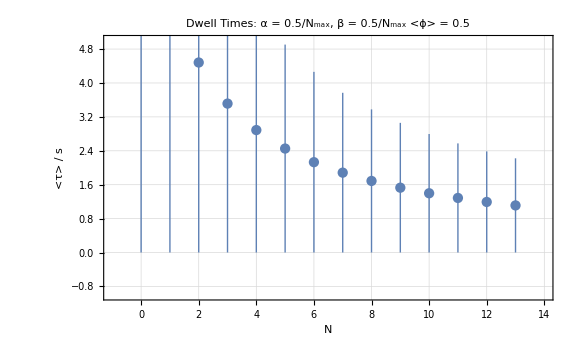

```mathematica
ListPlot[Table[Around[τDwell[k],τDwellSD[k]],{k,0,Nm}], PlotRange->{{-1,14},{-1,5}}, Frame->True, GridLines->Automatic, Axes->False,ImageSize->Large,FrameTicksStyle->Directive[12,Black], FrameLabel->{"N","<τ> / s"},LabelStyle->Directive[12,Black],PlotLabel->"Dwell Times: α = 0.5/N_max, β = 0.5/N_max
<ϕ> = 0.5",DataRange->{0,Nm}]
```

```mathematica
LangkonEQkoff =Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/DwellTimes/DwellTimes_Lang_kon=koff.dat"];
LangkonGTkoff =Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/DwellTimes/DwellTimes_Lang_kon.GT.koff.dat"];
LangkonLTkoff =Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/DwellTimes/DwellTimes_Lang_kon.LT.koff.dat"];
```

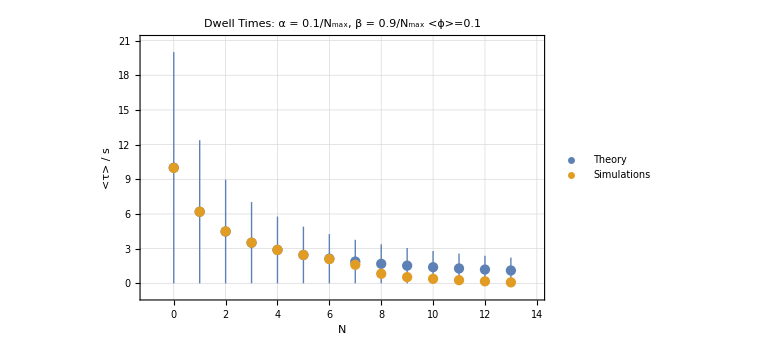

```mathematica
ListPlot[{Table[Around[τDwell[k],τDwellSD[k]],{k,0,Nm}],Around[LangkonLTkoff[[All,2]],LangkonEQkoff[[All,3]]]}, PlotRange->{{-1,14},{-1,21}}, Frame->True, GridLines->Automatic, Axes->False,ImageSize->Large,FrameTicksStyle->Directive[12,Black], FrameLabel->{"N","<τ> / s"},LabelStyle->Directive[12,Black],PlotLabel->"Dwell Times: α = 0.1/N_max, β = 0.9/N_max
<ϕ>=0.1",DataRange->{0,Nm},PlotLegends->Placed[LineLegend[{"Theory","Simulations"},LegendFunction->Panel],{{0.9,0.5},{0.5,0.3}}]]
```